```mathematica
gpu=Import[NotebookDirectory[]<>"4890.csv","CSV"];
cpu=Import[NotebookDirectory[]<>"Corei7.csv","CSV"];
```

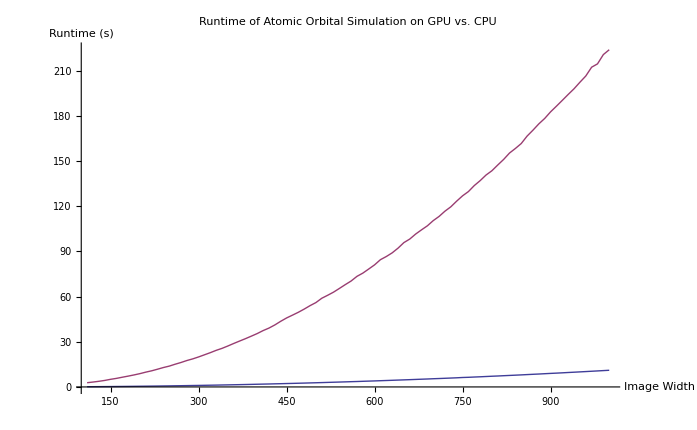

```mathematica
ListLinePlot[{gpu,cpu},PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,0},AxesLabel->{"Image Width","Runtime (s)"},PlotLabel->"Runtime of Atomic Orbital Simulation on GPU vs. CPU"]
```

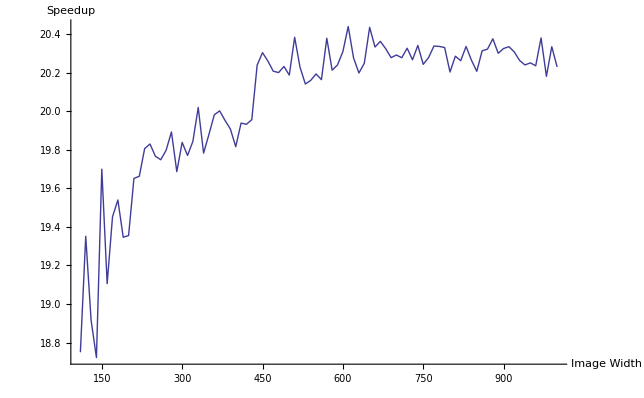

```mathematica
Speedup[a_,b_]:={a[[1]],b[[2]]/a[[2]]};
speedups=MapThread[Speedup,{gpu,cpu}];
ListLinePlot[speedups,PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,18},AxesLabel->{"Image Width","Speedup"}]
```

```mathematica
strongScaling:=Import[NotebookDirectory[]<>"strong.csv","CSV"];
```

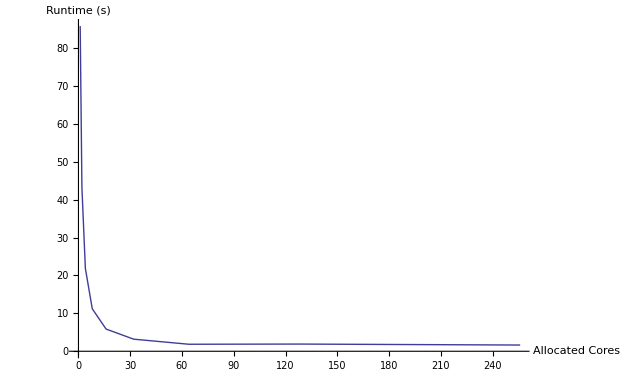

```mathematica
strongPlotOne=ListLinePlot[strongScaling,PlotStyle->Thick,AxesLabel->{"Allocated Cores","Runtime (s)"}]
```

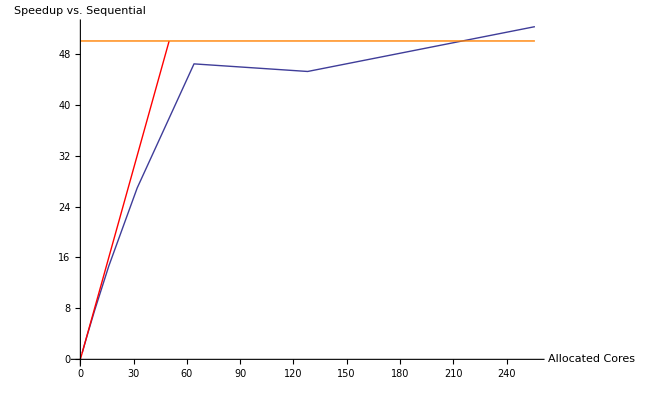

```mathematica
strongSpeedup={#[[1]],Last[First[strongScaling]]/#[[2]]}&/@strongScaling;
strongPlotTwo=Show[{ListLinePlot[strongSpeedup,PlotStyle->Thick,AxesLabel->{"Allocated Cores","Speedup vs. Sequential"}],Plot[x,{x,0,50},PlotStyle->{Red}],Plot[50,{x,0,256},PlotStyle->{Orange}]}]
```

```mathematica
Export["strongPlotOne.pdf",strongPlotOne]
```

strongPlotOne.pdf